# MATH7501 Practical 8 (Week 9), Semester 1-2021

## Topic: Sequences, Limits and Series

Author:  Aminath Shausan
Date: 30-04-2021

# Pre-Tutorial Activity

Students must have familiarised themselves with units 5 to 7 contents  of the reading materials for MATH7501

# Resources

Chapters 5 to 7 of course reader

https://reference.wolfram.com/language/tutorial/SeriesLimitsAndResidues.html#3309

# Q1 Construction of a function

Construct an example of a function f(x) so that:

• f (x) is defined for all real x;
• f' (x) exists and is negative for all x not equal to 0
• The point x = 0 is a local maximum of f.

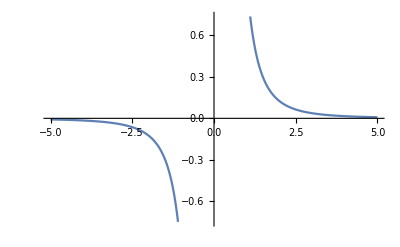

```mathematica
Plot[1/x^3, {x,-5,5}]
```

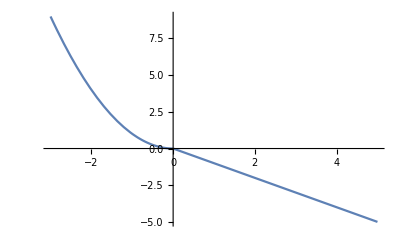

```mathematica
Plot[Piecewise[{{x^2,x<0},{-x,0<x}}],{x,-3,5}]
```

# Q2 Turning points of f(x)

The following graph describes a function f(x) on [-2, 6]. List all critical points in the interval (-2,6).
-Graphics-

Note that critical points occur when the first derivative is zero or undefined.
Critical Points and classifications.

```mathematica
x = -1 (discontinuity ) , (0, 1, 2 corners), 5 (vertical slope, point of inflexion), (the interval(2,3] derivative exists)
```

# Q3 Derivatives

Show why P(t)=C e^kt is the ONLY solution to the growth equation P'(t)=k P(t),with P(0)=C.

```mathematica
Suppose P(t)=A(t) e^kt , compute P'(t) and sub into P'(t)=k P(t)
```

```mathematica
P'(t) =A'(t)e^kt+kA(t)e^kt
```

```mathematica
A'(t)e^kt+kA(t)e^kt = kA(t)e^kt
A'(t)+kA(t)= kA(t)
this means A'(t) =0
therefore A(t)= constant (C)
And so P(t)=C e^kt
```

# Q4 Maclaurin series

Use Mathematica to plot the Maclaurin series approximations for e^x. 
Use these approximations to get an approximate value for e itself.

```mathematica
(* this computes Maclaurin series expansion of f(x) at x=0 upto order 4*)
Clear[f]
Series[f[x],{x,0,4}]
```

f[0]+f'[0] x+1/2 f''[0] x^2+1/6 f^(3)[0] x^3+1/24 f^(4)[0] x^4+O[x]^5

```mathematica
(* this computes Maclaurin series expansion of e^x at x=0 upto order 4*)
Series[Exp[x],{x,0,4}]
```

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

```mathematica
Normal[Series[Exp[x],{x,0,4}]]
```

1+x+x^2/2+x^3/6+x^4/24

```mathematica
Sum[x^n/n!,{n,0,4}]
```

1+x+x^2/2+x^3/6+x^4/24

```mathematica
(* first create a function to compute the Maclaurin series expansion of e^x at x=0 upto order n*)
Clear[f]
(*f[n_]:=Normal[Series[Exp[x],{x,0,n}]]*)
f[k_]:= Sum[x^n/n!,{n,0,k}]
```

```mathematica
f[5]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

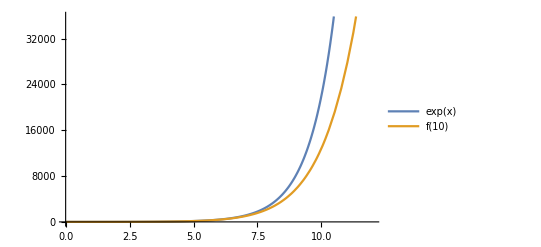

```mathematica
Plot[{Exp[x],f[10]},{x,0,12}, PlotLegends-> "Expressions"]
```

```mathematica
Manipulate[Plot[{f[k],Exp[x]},{x, 0, 10},  PlotLegends-> {"f(k)","e^x}"}],{k, 1, 10}]
```